```mathematica
(* 1- dataset of α and β *)
αdata={{0.5000000020621443,0.49999699726767755,0.49970371320248264,0.48470685324530366,0.4380603269387884,0.414991074941769,0.40731020595362083,0.40495,0.40456000000000014},{0.6000000020621442,0.5999974972676776,0.599752156180505,0.5853200828903069,0.5292680315491569,0.49926424259489977,0.4891817160827949,0.48596414961686407,0.4849446860589671},{0.6666666086958714,0.6666643113842685,0.6664432446786402,0.6524715144895905,0.590509097589787,0.5556156016469369,0.5438173337750933,0.5400497287606855,0.5388558455617956},{0.7500000020621442,0.7499979988522767,0.74980111094568,0.7364431142342496,0.6675042168929401,0.626232255258707,0.6121698976487877,0.607675038272152,0.6062505091549503},{0.9090909020621444,0.9090892016816402,0.9089263,0.8967441312623612,0.8157189385041558,0.7615490085943525,0.7427953456884953,0.7368307116677539,0.7349297488695207},{0.9803921065263472,0.9803906762212075,0.9802396522186773,0.9685607312623611,0.8826149385041556,0.8224051521405481,0.8014506857669599,0.7947372421152833,0.7926003982879933},{0.9951920432407088,0.9951907972676776,0.9950420522186771,0.9834654312623614,0.8965347385041562,0.8350510085943529,0.8136243456884955,0.8067580060436038,0.8045806508136303},{0.9975062020621442,0.9975047775232149,0.9973562522186771,0.9857964312623615,0.8987125385041566,0.8370285555286358,0.8155272733861672,0.8086371511120481,0.806452518015299},{0.9988900114599972,0.9988886744986657,0.9987403522186772,0.9871898312623619,0.9000149385041568,0.8382114191178833,0.8166656913201867,0.809761243637952,0.8075720858498913},{0.9994557020621443,0.9994541020622807,0.9993060522186771,0.9877585162835881,0.9005464277414373,0.8386946406141359,0.8171308853715952,0.8102214226876672,0.8080295675491966}};

βdata={{1.1754907046612933*^-8,1.4997770175452376*^-6,0.0001490250534954154,0.010558536560553503,0.20510744724476668,2.3662715503728378,24.58661827021307,248.70169999999993,2495.8922999999986},{1.1754907046612933*^-8,1.4997770175452376*^-6,0.00014932064504951742,0.011362546201852354,0.2405974376499903,2.8236730757562802,29.45603252711245,298.293868067345,2994.6188896910066},{2.2854339339468233*^-8,1.518285138381145*^-6,0.00014944773102869776,0.011794523150871292,0.26349236416757676,3.126429257651357,32.69582296396872,331.3346740229736,3327.0304837011395},{1.1754907046612933*^-8,1.4993892629701733*^-6,0.00014956311705049862,0.01224338690059289,0.2913040830144551,3.5025697149170854,36.73871916346641,372.6145308882861,3742.478585355081},{1.1754907046612933*^-8,1.5143834400411592*^-6,0.00014974969686706936,0.012890441933503064,0.34207898815129223,4.213995754044853,44.43738634817235,451.36066695005246,4535.415826948928},{2.6346052887722266*^-8,1.4876032192409818*^-6,0.00014974969686706936,0.013113441933503063,0.36390948815129226,4.530152453181804,47.879690508340204,486.6287024997233,4890.717854532409},{8.100493064359931*^-8,1.4997770175452376*^-6,0.00014974969686706936,0.013155441933503058,0.36837218815129213,4.595579754044855,48.59365634817236,493.9475657521283,4964.462597189455},{1.1754907046612933*^-8,1.4880129045453215*^-6,0.00014974969686706936,0.013161641933503054,0.36906758815129204,4.605802823908744,48.705265249855124,495.09178203818004,4975.992078807425},{4.078941987017619*^-8,1.4861462382482733*^-6,0.00014974969686706936,0.013165541933503055,0.36948328815129194,4.611916034516427,48.77201151339795,495.77609116353705,4982.887482307984},{1.1754907046612933*^-8,1.5142629563511925*^-6,0.00014974969686706936,0.013167348459177558,0.3696534956669053,4.614414238734443,48.79928624529476,496.05571447513023,4985.705218556087}};

(* 2- all values of two parameters *)
mpset={1,1.5,2,3,10,50,207,400,900,1836};
ωset={10^-4,10^-3,10^-2,10^-1,1,10,100,1000,10000};

(* 3- parameters *)
mp=1;
ω=10^-4;


(* 4- inputs *)
me=1;
M=mp+me;
n1=Flatten[Position[mpset,mp]];
n2=Flatten[Position[ωset,ω]];
α=Extract[Flatten[αdata[[n1,n2]]],1];
β=Extract[Flatten[βdata[[n1,n2]]],1];
γ=1/2*M*ω;
```

```mathematica
(*α=Rationalize[α,10^-50];
β=Rationalize[β,10^-50];*)

{α,β}=SetPrecision[{α,β},50];

(* 5- normalization factor *)
norm=(16*π^2*(Sqrt[π/2] (-2 α Sqrt[β]+E^(α^2/(2 β)) Sqrt[2 π] (α^2+β) Erfc[α/(Sqrt[2] Sqrt[β])]))/(128 β^(5/2) γ^(3/2)))^(-1/2);

(* 6- definitions *)
Γr[re_,rp_,r_]:=norm^2*Exp[-2 α r-2 β r^2-(2 γ)/M^2 (me^2 re^2+mp^2 rp^2+me mp (-r^2+re^2+rp^2))];

ΓCr[re_,rp_,r_]:=Γr[re,rp,r]-de[re]*dp[rp];
```

```mathematica
(* 7- first numerical integration*)
(*intrE[r_,re_]:=(E^(-2 r (α+r β)) (E^(-((2 (me re+mp (-r+re))^2 γ)/M^2))-E^(-((2 (me re+mp (r+re))^2 γ)/M^2))) M^2)/(4 mp (me+mp) γ);
iE=Integrate[r intrE[r,x],{r,0,Infinity},Assumptions->{x>0,α>0,β>0,γ>0,M>0,me>0,mp>0}];
de[re_?NumericQ]:=2 Pi norm^2/re iE/. x->re;

intrp[r_,rp_]:=(E^(-2 r (α+r β)) (E^(-((2 (mp rp+me (-r+rp))^2 γ)/M^2))-E^(-((2 (mp rp+me (r+rp))^2 γ)/M^2))) M^2)/(4 me (me+mp) γ);iP=Integrate[r intrp[r,y],{r,0,Infinity},Assumptions->{y>0,α>0,β>0,γ>0,M>0,me>0,mp>0}];
dp[rp_?NumericQ]:=2 Pi norm^2/rp iP/. y->rp;*)
```

```mathematica
intrE[r_,re_]:=(E^(-2 r (α+r β)) (E^(-((2 (me re+mp (-r+re))^2 γ)/M^2))-E^(-((2 (me re+mp (r+re))^2 γ)/M^2))) M^2)/(4 mp (me+mp) γ);

de[re_?NumericQ]:=(2*π)/re* norm^2*NIntegrate[r intrE[r,re],{r,0,∞}];

intrp[r_,rp_]:=(E^(-2 r (α+r β)) (E^(-((2 (mp rp+me (-r+rp))^2 γ)/M^2))-E^(-((2 (mp rp+me (r+rp))^2 γ)/M^2))) M^2)/(4 me (me+mp) γ);
dp[rp_?NumericQ]:=(2*π)/rp norm^2*NIntegrate[r intrp[r,rp],{r,0,∞}];
```

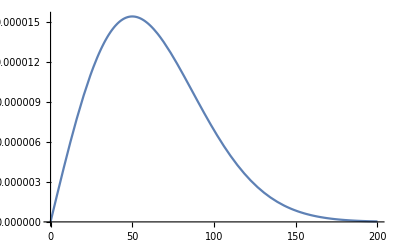

```mathematica
Plot[re de[re],{re,0,200},PlotRange->All]
```

```mathematica
Plot[rp dp[rp],{rp,0,200},PlotRange->All]
```

-Graphics-

```mathematica
(* 8- max values for re and rp *)
maxre=FindMaximum[ re de[re],{re,1/20},WorkingPrecision->100] 
maxrp=FindMaximum[ rp dp[rp],{rp,1/20000},WorkingPrecision->100]
```

```mathematica
(* 9- building subregions *)
rem=50;
rpm=50;
(*rpm=maxrp[[2,1,2]];*)
```

```mathematica
(* defining regions *)
loopn=7;
reg0=ImplicitRegion[0<=r<=100 rem && 0<=re<=100 rem && Abs[re-r]<=rp<=r+re,{r,re,rp}];
region[0]=RegionIntersection[reg0,ImplicitRegion[0<=r<=6 rem&&0<=re<=12 rem&&0<=rp<=rpm,{r,re,rp}]];reg12=region[0];Do[region[i]=RegionIntersection[reg0,ImplicitRegion[0<=r<=6 rem&&0<=re<=12 rem&&i rpm<=rp<=(i+1) rpm,{r,re,rp}]];
reg12=RegionUnion[reg12,region[i]];
,{i,loopn}];
region3=RegionDifference[reg0,reg12];

(* 10- integrals *)
int1=With[{p=8},-8*π^2*(Sum[NIntegrate[Γr[re,rp,r] re rp,Element[{r,re,rp},region[i]],AccuracyGoal->p,PrecisionGoal->p],{i,0,loopn}]+NIntegrate[Γr[re,rp,r] re rp,Element[{r,re,rp},region3],AccuracyGoal->p-2,PrecisionGoal->p-2])//AbsoluteTiming];
Print[" int1 ------->> ",int1[[2]],"            Time ------->> ",int1[[1]]];

int2=With[{p=8},-8*π^2*(Sum[NIntegrate[de[re]*dp[rp] re rp,Element[{r,re,rp},region[i]],AccuracyGoal->p,PrecisionGoal->p],{i,0,loopn}]+NIntegrate[de[re]*dp[rp] re rp,Element[{r,re,rp},region3],AccuracyGoal->p-2,PrecisionGoal->p-2])//AbsoluteTiming];
Print[" int2 ------->> ",int2[[2]],"            Time ------->> ",int2[[1]]];

int3=With[{p=8},-8*π^2*(Sum[NIntegrate[ΓCr[re,rp,r] re rp,Element[{r,re,rp},region[i]],AccuracyGoal->p,PrecisionGoal->p],{i,0,loopn}]+NIntegrate[Γr[re,rp,r] re rp,Element[{r,re,rp},region3],AccuracyGoal->p-2,PrecisionGoal->p-2])//AbsoluteTiming];
Print[" int3 ------->> ",int3[[2]],"        Time ------->> ",int3[[1]]];


Print[int2+int3]
```

int1 ------->> -0.5            Time ------->> 1.37199

int2 ------->> -0.0112811            Time ------->> 145.047

int3 ------->> -0.488719        Time ------->> 348.281

{493.328,-0.5}